# Cosmic-ray upscattered inelastic dark matter

This notebook contains the calculations, analysis and figures for the paper arXiv:2108.00583

## Introduction

This notebook calculates the flux and observable rates of cosmic-ray upscattered inelastic dark matter.

The halo dark matter is assumed to be in the low mass state χ_1 with mass m_χ_1, this can be upscattered to a heavier state χ_2 with mass m_χ_2=m_χ_1+δ
(m_χ_1 and δ are taken as the model parameters, m_χ_2 is not used so all refereces to mass can be assumed to be m_χ_1) 

Throughout the calculations units are generally assumed to be in GeV, except where explicitly named in the variable.

- Gray (initialization) cells can be evaluated automatically
- Red cells are the main computations and can take minutes to run
- Blue cells create plots
- Purple cells create output files

## Constants

```mathematica
ℏc=0.19732698;(*GeV fm*)
Centimeter= 1/ℏc 10^13/GeV;
𝒸=2.997925 10^8;
Second=𝒸 10^2 Centimeter;
Kilogram=𝒸^2/(1.602 10^-19)GeV/10^9;
kpc=3.086 10^21 Centimeter;
KilogramDay=(1Kilogram)(24 3600Second);
tonneYr=365250 KilogramDay;
mp=0.93827208816//SetPrecision[#,11]&;
Deff=0.997kpc;
ρX=0.3 GeV/Centimeter^3;
unitsCM2S=(Centimeter^2/cm^2)(Second/s);
amu=mp/1.00727647//SetPrecision[#,10]&;
mn=0.93956542052//SetPrecision[#,11]&;
Me=510.998950keV;
```

#### Set plot styles and custom plot functions

```mathematica
SetOptions[#,Frame->True,FrameStyle->Directive[Black,18,FontFamily->Times,Thickness[.004]],AspectRatio->1,PlotStyle->Thick,ImageSize->400]&@{Plot,LogPlot,LogLogPlot,LogLinearPlot,ListPlot,ListLogPlot,ListLogLogPlot,ListLogLinearPlot};
SetOptions[#,Frame->True,LabelStyle->Directive[Black,16,FontFamily->Times,Thickness[.004]],AspectRatio->1,ImageSize->400]&@{Histogram,MatrixPlot};
logSpace[a_, b_, n_] := 10.0^Range[Log10[a], Log10[b], (Log10[b] - Log10[a])/(n - 1)];

topLeft[x_] := Placed[x, {Scaled[{.38, .95}], {.9, 1}}];
topRight[x_] := Placed[x,{Scaled[{.95, .95}], {.9, 1}}];
Legend//Clear;
Legend[legendList_,opt:OptionsPattern[{Position->"Right",Type->"Line",LineLegend}]] := Module[{f},
If[OptionValue[Type]=="Line",
f=LineLegend;];
If[OptionValue[Type]=="Swatch",
f=SwatchLegend;];
If[OptionValue[Position]=="Right",
   f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topRight//Return];
If[OptionValue[Position]=="Left",
   f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//topLeft//Return];

f[ Style[#, 14, FontFamily -> "Times"] & /@ legendList, FilterRules[{opt},Except[{Position,Type}]] ]//Placed[#,OptionValue[Position]]&//Return;
];

LogTicks//Clear;
LogTicks[min_,max_,step_] := Block[{lmin, lmax, t},
   lmin = Floor[Log10[min]];
   lmax = Floor[Log10[max]];
   t=0;
   Return[{Join[
      Table[{10^i, If[Mod[++t,step]==0,Superscript[10, i],Null], {0.012, 0}}, {i, Floor[lmin], Ceiling[lmax]}], (Flatten[#1, 1] &)[
       Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], 
        Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]], 
     Join[Table[{10^i, Null, {0.012, 0}}, {i, Floor[lmin], 
     Ceiling[lmax]}], (Flatten[#1, 1] &)[ Table[{i*10^j, Null, {0.006, 0}}, {j, Floor[lmin], Ceiling[lmax], 1}, {i, 0.1, 0.9, 0.1}]]]}  ]
];
LogTicks[min_, max_] := LogTicks[min,max,1];
```

## Cosmic-ray fluxes

### Import spectra

We will consider cosmic-ray protons and helium, define their mass, charge, atomic number and spin:

```mathematica
mi  = {mp, 4.002602*amu};
Zei = {1,2};
Ai  = {1,4};
ji  = {0.5,0};
```

Import CR flux data tables and create interpolation functions:

```mathematica
NotebookDirectory[]//SetDirectory;
protonLISdata=Import["data/TABLE_Protons_R.txt","Table"]//Drop[#,1]&;
HeLISdata=Import["data/TABLE_Helium_R.txt","Table"]//Drop[#,1]&;
dIdR={Interpolation[protonLISdata,InterpolationOrder->1],Interpolation[HeLISdata,InterpolationOrder->1]};
```

Plot raw data, which is a function of rigidity:

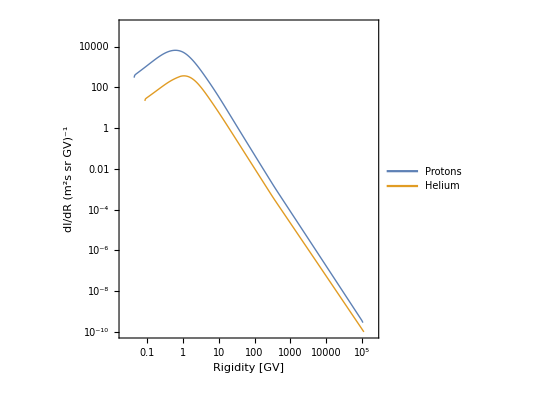

```mathematica
ListLogLogPlot[
{protonLISdata,HeLISdata},Joined->True,
FrameLabel->{"Rigidity [GV]","dI/dR (m^2s sr GV)^-1"},
PlotRange->{10^-10,10^5},
PlotLegends->Legend[{"Protons","Helium"}]]
```

### Converting to kinetic energy

Functions for rigidity (R) in terms of kinetic energy (T) and vise-versa:

```mathematica
Rt[T_,ii_]:=(√(T^2+2mi⟦ii⟧ T))/Zei⟦ii⟧
```

```mathematica
TR[R_,jj_]:=√((mi⟦jj⟧)^2+(R Zei⟦jj⟧)^2)-mi⟦jj⟧
```

Max kinetic energy in provided data files:

```mathematica
TdatMin={TR[protonLISdata⟦1,1⟧,1],TR[HeLISdata⟦1,1⟧,2]}
TdatMax={TR[protonLISdata⟦-1,1⟧,1],TR[HeLISdata⟦-1,1⟧,2]}
```

{0.000999971,0.00399668}

{105099.,420396.}

```mathematica
dRdT=D[√(T^2+2mi T),T]/Zei
```

{(1.8765441763+2 T)/(2 √(1.8765441763 T+T^2)),(7.4568+2 T)/(4 √(7.4568 T+T^2))}

Converting to function of kinetic energy and giving flux in units of GeV^2

```mathematica
dϕdT[t_?NumericQ,i_?IntegerQ]:=Evaluate[(4π)/100^2 1/(Centimeter^2 Second GeV)]dIdR⟦i⟧[Rt[t ,i]] (dRdT⟦i⟧/.T->t)
```

```mathematica
Centimeter^2 Second GeV dϕdT[10,1]
```

0.0336674

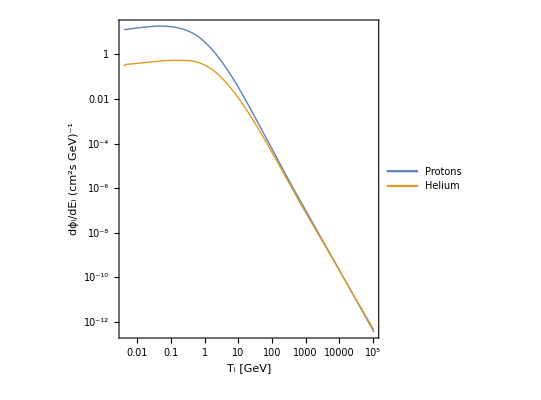

```mathematica
LogLogPlot[{Centimeter^2 Second GeVdϕdT[t,1],Centimeter^2 Second GeV dϕdT[t,2]},{t,TdatMin//Max,TdatMax//Min},FrameTicksStyle->Directive[Black,15],FrameTicks->Automatic,PlotRange->All,AspectRatio->1,PlotLegends->Legend[{"Protons","Helium"}],FrameLabel->{Style["T_i [GeV]",18,Black,FontFamily->Times],Style["dϕ_i/dE_i (cm^2s GeV)^-1",18,Black,FontFamily->Times]}]
```

Build flux tables:

```mathematica
pFlux=Table[{T,dϕdT[T,1] GeV^-2},{T,logSpace[TdatMin⟦1⟧,TdatMax⟦1⟧,800]}]//Interpolation[#,InterpolationOrder->1]&;
heFlux=Table[{T,dϕdT[T,2] GeV^-2},{T,logSpace[TdatMin⟦2⟧,TdatMax⟦2⟧,800]}]//Interpolation[#,InterpolationOrder->1]&;
```

```mathematica
dϕdT[75326.23378158691,1]
```

2.38172×10^-64 GeV^2

```mathematica
pFlux[99]
```

1.52574×10^-56

## CRDM flux

### Kinematic limits

Find inelastic limits:

p_i= p_i'+ p_x
p_i'^2 = p_i^2+p_x^2-2 p_i p_x cosθ
use p^2=E^2-m^2 and E = T + m

```mathematica
Solve[((Tip+mii)^2-mii^2)==((Ti+mii)^2-mii^2)+((Tx+mxp)^2-mxp^2)+2 √(((Ti+mii)^2-mii^2)((Tx+mxp)^2-mxp^2))/.{mxp->mx+δ,Tip->Ti-Tx-δ},{Tx}]//FullSimplify
```

{{Tx→(2 mx Ti (2 mii+Ti)-2 (mii (mii+mx)+mx Ti) δ+(mii+mx+Ti) δ^2-√(-Ti (2 mii+Ti) (-2 mx Ti+2 (mii+mx) δ+δ^2) (2 mx (Ti-δ)-δ^2+2 mii (2 mx+δ))))/(2 (mii+mx)^2+4 mx Ti)},{Tx→(2 mx Ti (2 mii+Ti)-2 (mii (mii+mx)+mx Ti) δ+(mii+mx+Ti) δ^2+√(-Ti (2 mii+Ti) (-2 mx Ti+2 (mii+mx) δ+δ^2) (2 mx (Ti-δ)-δ^2+2 mii (2 mx+δ))))/(2 (mii+mx)^2+4 mx Ti)}}

```mathematica
1/(2 (mii)^2+4 mx Ti)(2 mx Ti (2 mii+Ti)-2 (mii (mii)+mx Ti) δ+(Ti) δ^2-√(-Ti (2 mii+Ti) (-2 mx Ti+2 (mii) δ) (2 mx (Ti)+2 mii (2 mx+δ))))//FullSimplify
```

1/(2 (mii^2+2 mx Ti))(2 mx Ti (2 mii+Ti)-2 (mii^2+mx Ti) δ+Ti δ^2-2 √(Ti (2 mii+Ti) (mx Ti-mii δ) (mx Ti+mii (2 mx+δ))))

Define functions for kinematic limits:

```mathematica
TxMin[Ti_?NumericQ,mii_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=
If[δ==0,0,
1/(2 (mii+mx)^2+4 mx Ti)(2 mx Ti (2 mii+Ti)-2 (mii (mii+mx)+mx Ti) δ+(mii+mx+Ti) δ^2-√(-Ti (2 mii+Ti) (-2 mx Ti+2 (mii+mx) δ+δ^2) (2 mx (Ti-δ)-δ^2+2 mii (2 mx+δ))))]
```

```mathematica
TxMax[Ti_?NumericQ,mii_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=
1/(2 (mii+mx)^2+4 mx Ti)(2 mx Ti (2 mii+Ti)-2 (mii (mii+mx)+mx Ti) δ+(mii+mx+Ti) δ^2+√(-Ti (2 mii+Ti) (-2 mx Ti+2 (mii+mx) δ+δ^2) (2 mx (Ti-δ)-δ^2+2 mii (2 mx+δ))))
```

```mathematica
TxMinGlobal[mx_,δ_]:=δ^2/(2mx)
```

Minimum incoming energy to produce outgoing Tx:

```mathematica
Solve[((Tip+mii)^2-mii^2)==((Ti+mii)^2-mii^2)+((Tx+mxp)^2-mxp^2)+2 √(((Ti+mii)^2-mii^2)((Tx+mxp)^2-mxp^2))/.{mxp->mx+δ,Tip->Ti-Tx-δ},{Ti}]//FullSimplify
```

{{Ti→1/2 (-2 mii+Tx+δ+(√(Tx (2 mx+Tx+2 δ) (2 mx Tx-δ^2) (4 mii^2+2 mx Tx-δ^2)))/(-2 mx Tx+δ^2))},{Ti→1/2 (-2 mii+Tx+δ+(√(Tx (2 mx+Tx+2 δ) (2 mx Tx-δ^2) (4 mii^2+2 mx Tx-δ^2)))/(2 mx Tx-δ^2))}}

```mathematica
TiMin[Tx_?NumericQ,mii_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=
If[δ>δMax[Tx,mx],∞,
1/2 (-2 mii+Tx+δ+(√(Tx (2 mx+Tx+2 δ) (2 mx Tx-δ^2) (4 mii^2+2 mx Tx-δ^2)))/(2 mx Tx-δ^2))];
```

Find max delta:

```mathematica
Solve[((16 mii mx Tx-8 mx Tx^2-8 mx Tx δ-8 mii δ^2+4 Tx δ^2+4 δ^3)^2-4 (8 mx Tx-4 δ^2) (-4 mii^2 Tx^2-8 mii mx Tx^2-4 mx^2 Tx^2-8 mii^2 Tx δ-8 mii mx Tx δ-4 mii^2 δ^2+4 mii Tx δ^2+4 mx Tx δ^2+4 mii δ^3-δ^4))==0,δ]
```

{{δ→1/2 (-2 mx-Tx)},{δ→-√2 √mx √Tx},{δ→√2 √mx √Tx},{δ→-√2 √(2 mii^2+mx Tx)},{δ→√2 √(2 mii^2+mx Tx)}}

```mathematica
δMax[Tx_,mx_]:=√(2 mx Tx)
```

Global Ti minimum:

```mathematica
gMin=D[1/2 (-2 mii+Tx+δ+(√(Tx (2 mx+Tx+2 δ) (2 mx Tx-δ^2) (4 mii^2+2 mx Tx-δ^2)))/(2 mx Tx-δ^2)),Tx]==0//Solve[#,Tx]&
```

{{Tx→((2 mii-δ) δ (mx+δ))/(2 mx (mii-mx-δ))},{Tx→(δ (2 mii+δ) (mx+δ))/(2 mx (mii+mx+δ))},{Tx→(-2 mii δ-δ^2)/(2 (mii-mx))},{Tx→(-2 mii δ+δ^2)/(2 (mii+mx))}}

```mathematica
1/2 (-2 mii+Tx+δ+(√(Tx (2 mx+Tx+2 δ) (2 mx Tx-δ^2) (4 mii^2+2 mx Tx-δ^2)))/(2 mx Tx-δ^2))/.gMin//Simplify[#,Assumptions->{mx>0,δ>0,mii>0}]&
```

{Piecewise[{{-((2 mii-δ) (2 mx+δ))/(2 mx), 2 mii≤δ⊻2 mii≤2 mx+δ}, {(mii δ (-2 mii+δ))/(2 mx (-mii+mx+δ)), True}}],(δ (2 mii+2 mx+δ))/(2 mx),Piecewise[{{-2 mii, 2 mii>2 mx+δ}, {-(δ (2 mx+δ))/(2 (mii-mx)), True}}],-((2 mii+2 mx+δ) (2 mii-δ+Abs[-2 mii+δ]))/(4 (mii+mx))}

```mathematica
TiMinGlobal[mii_?NumericQ,mx_?NumericQ,δ_?NumericQ]:=(δ (2 mii+2 mx+δ))/(2 mx)
```

Max δ for a given Ti:

```mathematica
Solve[(δ (2 mii+2 mx+δ))/(2 mx)==TiMi,δ]
```

{{δ→-mii-mx-√(mii^2+2 mii mx+mx^2+2 mx TiMi)},{δ→-mii-mx+√(mii^2+2 mii mx+mx^2+2 mx TiMi)}}

```mathematica
δMaxTi[Ti_,mii_,mx_]:=-mii-mx+√(mii^2+2 mii mx+mx^2+2 mx Ti)
```

#### Sample phase-space plots

Plot limits of kinematic variables for some example values:

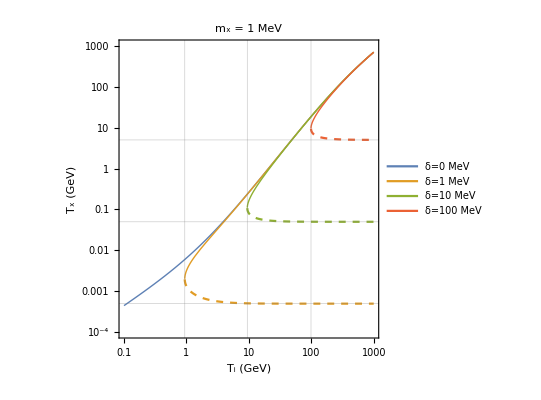
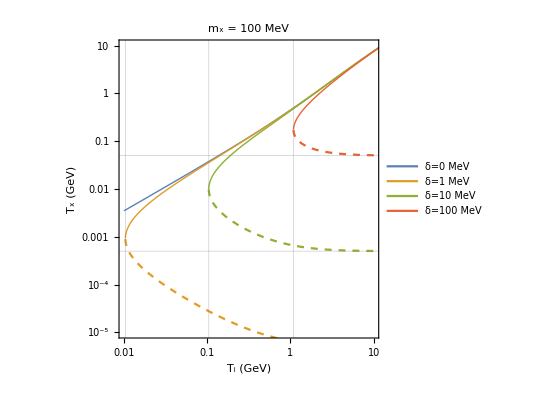

```mathematica
{Show[LogLogPlot[{TxMax[Ti,mp,.001,0],TxMax[Ti,mp,.001,0.001],TxMax[Ti,mp,.001,.01],TxMax[Ti,mp,.001,.1]},{Ti,.1,1000},FrameLabel->{"T_i (GeV)","T_x (GeV)"},PlotLabel->Style["m_x = 1 MeV",16,Black],
PlotRange->{{.1,1000},{.0001,1000}},
PlotLegends->Legend[{"δ=0 MeV","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.2,.8}],
GridLines->{{TiMinGlobal[mp,.001,.001],TiMinGlobal[mp,.001,.01],TiMinGlobal[mp,.001,.1]},{TxMinGlobal[.001,.001],TxMinGlobal[.001,.01],TxMinGlobal[.001,.1]}}],
LogLogPlot[{0,TxMin[Ti,mp,.001,0.001],TxMin[Ti,mp,.001,.01],TxMin[Ti,mp,.001,.1]},{Ti,.1,1000},PlotStyle->Dashed,FrameLabel->{"T_i (GeV)","T_x (GeV)"}]],
Show[LogLogPlot[{TxMax[Ti,mp,.1,0],TxMax[Ti,mp,.1,0.001],TxMax[Ti,mp,.1,.01],TxMax[Ti,mp,.1,.1]},{Ti,.01,50},FrameLabel->{"T_i (GeV)","T_x (GeV)"},PlotLabel->Style["m_x = 100 MeV",16,Black],
PlotRange->{{.01,10},{.00001,10}},
PlotLegends->Legend[{"δ=0 MeV","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.2,.8}],
GridLines->{{TiMinGlobal[mp,.1,.001],TiMinGlobal[mp,.1,.01],TiMinGlobal[mp,.1,.1]},{TxMinGlobal[.1,.001],TxMinGlobal[.1,.01],TxMinGlobal[.1,.1]}}],
LogLogPlot[{0,TxMin[Ti,mp,.1,0.001],TxMin[Ti,mp,.1,.01],TxMin[Ti,mp,.1,.1]},{Ti,.01,50},PlotStyle->Dashed,FrameLabel->{"T_i (GeV)","T_x (GeV)"}]]}
```

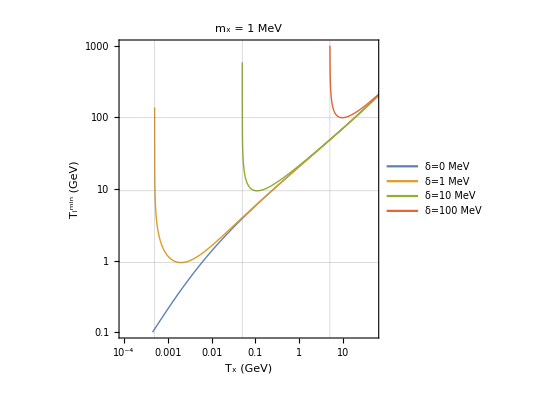
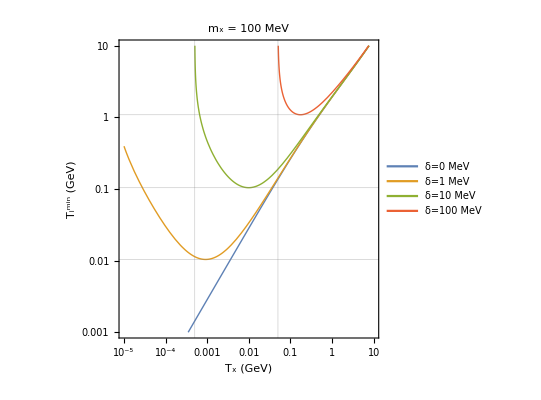

```mathematica
{LogLogPlot[{TiMin[Ti,mp,.001,0],TiMin[Ti,mp,.001,0.001],TiMin[Ti,mp,.001,.01],TiMin[Ti,mp,.001,.1]},{Ti,.0001,100},FrameLabel->{"T_x (GeV)","T_i^min (GeV)"},PlotLabel->Style["m_x = 1 MeV",16,Black],
PlotRange->{{.0001,50},{.1,1000}},
PlotLegends->Legend[{"δ=0 MeV","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.8,.2}],
GridLines->{{TxMinGlobal[.001,.001],TxMinGlobal[.001,.01],TxMinGlobal[.001,.1]},{TiMinGlobal[mp,.001,.001],TiMinGlobal[mp,.001,.01],TiMinGlobal[mp,.001,.1]}}],
LogLogPlot[{TiMin[Ti,mp,.1,0],TiMin[Ti,mp,.1,0.001],TiMin[Ti,mp,.1,.01],TiMin[Ti,mp,.1,.1]},{Ti,.00001,10},FrameLabel->{"T_x (GeV)","T_i^min (GeV)"},PlotLabel->Style["m_x = 100 MeV",16,Black],
PlotRange->{{.00001,10},{.001,10}},
PlotLegends->Legend[{"δ=0 MeV","δ=1 MeV","δ=10 MeV","δ=100 MeV"},Position->{.8,.2}],
GridLines->{{TxMinGlobal[.1,.001],TxMinGlobal[.1,.01],TxMinGlobal[.1,.1]},{TiMinGlobal[mp,.1,.001],TiMinGlobal[mp,.1,.01],TiMinGlobal[mp,.1,.1]}}]}
```

### Form factors

#### Helm

Standard definition of the Helm form factor:
q = momentum transfer in GeV
A = atomic number of target nuclei

```mathematica
Fhelm[q_,A_]=
Piecewise[{
			{3(Sin[(q r)/ℏc]-((q r)/ℏc)Cos[(q r)/ℏc])/((q r)/ℏc)^3 Exp[(-((q s)/ℏc)^2)/2]/.{r->((1.23 A^(1/3)-.6)^2+7/3 π^2(0.52)^2-5(0.9)^2)^(1/2),s->0.9},4>q>0},
		{0,q>4}
},1];
```

#### dipole form factor

Dipole form of the form factor:

```mathematica
Gi[q2_,Λi_]:=(1+q2/Λi^2)^-2
```

Where Λ comes from the charge radius:

```mathematica
Λi={0.770,0.410};
```

#### Nuclear response functions

```mathematica
WM00[qGeV_,A_]:=
Switch[A,
1,0.0397887 Gi[qGeV^2,Λi⟦1⟧]^2,
4,0.31831 Gi[qGeV^2,Λi[[2]]]^2,
_,((4π)/1 4)^-1 A^2 Fhelm[qGeV,A]^2
];
```

```mathematica
FM[qGeV_,A_,jN_]:=(4π)/(2jN+1)4WM00[qGeV,A]
```

### CR-DM cross section

Reduced mass:

```mathematica
μ[m1_,m2_]:=(m1 m2)/(m1+m2)
```

Functions for NR cross section:

```mathematica
σXP[g_,mx_,mϕ_,kk_:0]:=(4 g^4 μ[mx,mp]^2)/(π mϕ^4(1+4 kk^2/mϕ^2))/Centimeter^2/GeV^2
```

Coupling for a given cross section:

```mathematica
gg[σ_,mx_,mϕ_]:=((σ π mϕ^4)/(4 μ[mx,mp]^2)Centimeter^2 GeV^2 )^(1/4)
```

Full differential cross section (A^2 enhancement is included in the structure factor F_M):
	Tx = DM kinetic energy
	Ti  = incoming CR energy 
	mx = mass of dark matter
	δ = mass splitting
	gxi = to mediator coupling (takes x and nucleon coupling as the same)
	mA = mass of mediator
	iS = species of CR (1 = proton, 2 = neutron)
Units of returned differential cross section are GeV^-3

```mathematica
dσidTxVector[Tx_?NumericQ,Ti_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ,iS_?IntegerQ]:=
(
(gxi^4 (4 mx (mi⟦iS⟧+Ti)^2-2 ((mi⟦iS⟧+mx)^2+2 mx Ti) Tx+2 mx Tx^2-4 mx (mi⟦iS⟧+Ti) δ+(mx-Tx) δ^2)) / (2 π Ti (2 mi⟦iS⟧+Ti)(mA^2+2 mx Tx-δ^2)^2 GeV^3)
)FM[√(2 mx Tx-δ^2),Ai⟦iS⟧,ji⟦iS⟧]
```

### Define flux

Function for the upscattered χ_2dark matter flux, contributions from protons and helium included.
	Tx2 = flux is computed for the χ_2DM kinetic energy Tx2
	mx = mass of dark matter
	δ = mass splitting
	gxi = to mediator coupling (takes x and nucleon coupling as the same)
	mA = mass of mediator
Units of returned flux are GeV^2

```mathematica
dϕX2dTx2[Tx2_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ]:=
Deff*(ρX/(mx GeV))(
If[TxMin[TdatMax⟦1⟧,mi⟦1⟧,mx,δ]>Tx2,0,
	NIntegrate[
	pFlux[Tii] dσidTxVector[Tx2,Tii,mx,δ,gxi,mA,1] GeV^3,
	{Tii,  Max[TdatMin⟦1⟧,TiMin[Tx2,mi⟦1⟧,mx,δ]],  Max[TdatMax⟦1⟧,TiMin[Tx2,mi⟦1⟧,mx,δ]]  },
	Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->∞,PrecisionGoal->3]
]
+If[TxMin[TdatMax⟦2⟧,mi⟦2⟧,mx,δ]>Tx2,0,
	NIntegrate[
	heFlux[Tii] dσidTxVector[Tx2,Tii,mx,δ,gxi,mA,2] GeV^3,
	{Tii,Max[TdatMin⟦2⟧,TiMin[Tx2,mi⟦2⟧,mx,δ]],Max[TdatMax⟦2⟧,TiMin[Tx2,mi⟦2⟧,mx,δ]]},
	Method->{"GlobalAdaptive","SymbolicProcessing"->0},AccuracyGoal->∞,PrecisionGoal->3]
]
)
```

When the mediator mass is small and mass splitting is large the spectrum becomes sharply peaked, this function finds that peak and does a better job sampling the spectra:
	variable are same as above, but with the flux returned for nPoints sampled between {TX2MIN, TX2MAX}

```mathematica
dϕX2dTx2list[TX2MIN_?NumericQ,TX2MAX_?NumericQ,mx_?NumericQ,δ_?NumericQ,gxi_?NumericQ,mA_?NumericQ,nPoints_?NumericQ]:=
Module[{Tx2Points,maxF,TMIN,TMAX},
If[TX2MIN<TxMin[TdatMax⟦1⟧,mi⟦1⟧,mx,δ],TMIN=TxMin[TdatMax⟦1⟧,mi⟦1⟧,mx,δ];,TMIN=TX2MIN];
If[TX2MAX>TxMax[TdatMax⟦1⟧,mi⟦1⟧,mx,δ],TMAX=TxMax[TdatMax⟦1⟧,mi⟦1⟧,mx,δ];,TMAX=TX2MAX];
(*More careful sampling if there are sharp peaks*)
If[mA<.01&&δ>.002,
maxF=Txp/.(NMaximize[{dϕX2dTx2[Txp,mx,δ,gxi,mA] GeV^-2,Txp>TMIN},Txp,PrecisionGoal->3,Method->"NelderMead"][[2,1]]);
Tx2Points=Join[logSpace[TMIN,Min[maxF,TMAX],2nPoints/8//Round],logSpace[maxF,Min[400(maxF-TMIN)+maxF,TMAX],2nPoints/8//Round],logSpace[Min[401(maxF-TMIN)+maxF,TMAX],TMAX,nPoints/2//Round]]//Sort//DeleteDuplicates;
,
Tx2Points=logSpace[TMIN,TMAX,nPoints]];
ParallelTable[{Tx2,dϕX2dTx2[Tx2,mx,δ,gxi,mA] GeV^-2},
{Tx2,Tx2Points}]//Return
]
```

### Up-scattered DM spectra

#### Calculate

Choose couplings around sensitivity limit but that have round numbers:

```mathematica
σXP[√(.5),.1,1]
```

1.01218×10^-30

```mathematica
gxHeavy=√(.5);
```

```mathematica
σXP[√(.001),.001,.001]
```

4.94718×10^-28

```mathematica
gxLight=√(.001);
```

```mathematica
datFluxVecElas={
ParallelTable[{Tx,dϕX2dTx2[Tx,0.001,0,gxLight,.001]Tx GeV(unitsCM2S cm^2 s)},
{Tx,logSpace[10^-5,100,200]}]
,
ParallelTable[{Tx,dϕX2dTx2[Tx,0.100,0,gxHeavy,1.00]Tx GeV(unitsCM2S cm^2 s)},
{Tx,logSpace[10^-5,100,200]}]};
```

```mathematica
With[{MX=10^-3,MA=10^-3},

datFluxVecM1MeVlight={
ParallelTable[
 {Tx,dϕX2dTx2[Tx,MX,.0001,gxLight,MA] Tx GeV (unitsCM2S cm^2 s)},
{Tx,logSpace[TxMin[0.99TdatMax⟦1⟧,mi⟦1⟧,MX,.0001],10,400]}]
,
	ParallelTable[
 {Tx,dϕX2dTx2[Tx,MX,.001,gxLight,MA] Tx GeV (unitsCM2S cm^2 s)},
{Tx,logSpace[TxMin[0.99TdatMax⟦1⟧,mi⟦1⟧,MX,.001],10,400]}]
,
ParallelTable[{Tx,
dϕX2dTx2[Tx,MX,0.01,gxLight,MA]Tx GeV (unitsCM2S cm^2 s)},
{Tx,logSpace[TxMin[0.99TdatMax⟦1⟧,mi⟦1⟧,MX,.010],10,400]}]
,
dϕX2dTx2list[.1,10,MX,.1,gxLight,MA,400]//{#[[All,1]],#[[All,1]]*#[[All,2]]*unitsCM2S GeV^3 cm^2 s}&//Thread}];
```

#### Plot spectra

```mathematica
commonOptions={Joined->True,
FrameTicks->{LogTicks[10^-16,1],LogTicks[10^-6,10^2]},
PlotRange->{{10^-5,20},{10^-9,10^-2}},
FrameLabel->{"CRDM kinetic energy, T_χ(GeV)","CRDM flux, T_χ dϕ/dT_χ (cm^-2s^-1)"}};
```

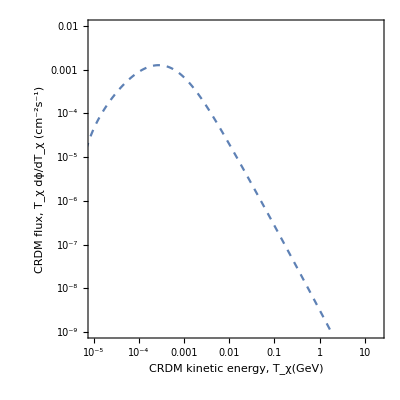

```mathematica
inelasFluxPlot0=ListLogLogPlot[
datFluxVecM1MeVlight[[1]],PlotStyle->Dashed,
commonOptions]
```

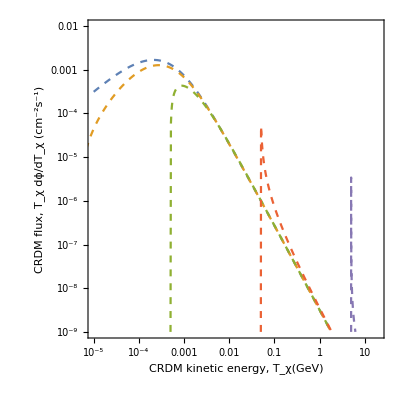

```mathematica
inelasFluxPlot1MeVlight=ListLogLogPlot[
Join[{datFluxVecElas⟦1⟧},datFluxVecM1MeVlight],PlotStyle->Dashed,
commonOptions];
inelasFluxPlot1MeVlight
```